```mathematica
({{1, ⅈ, 0}, {1, -ⅈ, 0}, {0, 0, 1}}).({{a1}, {a2}, {a3}})//MatrixForm
```

(a1+ⅈ a2
a1-ⅈ a2
a3)

```mathematica
(*холестерик*)
e=({{e2 + Δe/2 +Δe Cos[2θ], Δe Sin[2θ], 0}, {Δe Sin[2θ], e2 + Δe/2 -Δe Cos[2θ], 0}, {0, 0, e33}});
```

```mathematica
MatrixForm[FullSimplify[({{1, ⅈ, 0}, {1, -ⅈ, 0}, {0, 0, 1}}).({{e2 + Δe/2 +Δe Cos[2θ], Δe Sin[2θ], 0}, {Δe Sin[2θ], e2 + Δe/2 -Δe Cos[2θ], 0}, {0, 0, e33}}).({{1/2, 1/2, 0}, {1/(2 ⅈ), -1/(2 ⅈ), 0}, {0, 0, 1}})]]
```

```mathematica
(*НОВЫЙ ОБЩИЙ ВИД ТЕНЗОРА*)
MatrixForm[FullSimplify[({{1, ⅈ, 0}, {1, -ⅈ, 0}, {0, 0, 1}}).({{e+A Cos[2q z], ⅈ Y+A Sin[2q z], B Cos[q z+r ]}, {A Sin[2q z]-ⅈ Y, e-A Cos[2q z], B  Sin[q z+r ]}, {Subscript[B, c] Cos[q z+Subscript[r, c] ], Subscript[B, c]  Sin[q z+Subscript[r, c] ], e3}}).({{1/2, 1/2, 0}, {1/(2 ⅈ), -1/(2 ⅈ), 0}, {0, 0, 1}})]]
```

(e+Y | A ⅇ^(2 ⅈ q z) | B ⅇ^(ⅈ (r+q z))
A ⅇ^(-2 ⅈ q z) | e-Y | B ⅇ^(-ⅈ (r+q z))
1/2 ⅇ^(-ⅈ (q z+r_c)) B_c | 1/2 ⅇ^(ⅈ (q z+r_c)) B_c | e3)

```mathematica
ϵ=({{e+Y, A ⅇ^(2 ⅈ q z), B ⅇ^(ⅈ (r+q z))}, {A ⅇ^(-2 ⅈ q z), e-Y, B ⅇ^(-ⅈ (r+q z))}, {1/2 ⅇ^(-ⅈ (q z+Subscript[r, c])) Subscript[B, c], 1/2 ⅇ^(ⅈ (q z+Subscript[r, c])) Subscript[B, c], e3}});
h=({{ⅈ dz, 0, kp}, {0, -ⅈ dz, -km}, {km/2, -kp/2, 0}});
ψ=({{ψp[z]}, {ψm[z]}, {ψ3[z]}});
Simplify[MatrixForm[Simplify[Subscript[k, 0]^2*ϵ.ψ-h.h.ψ]/.kp-> kperp ⅇ^(ⅈ ϕ)/.km-> kperp ⅇ^(-ⅈ ϕ)]/.kperp-> kp]
```

(-ⅈ dz ⅇ^(ⅈ ϕ) kp ψ3[z]+1/2 ⅇ^(2 ⅈ ϕ) kp^2 ψm[z]+(dz^2-kp^2/2) ψp[z]+k_0^2 (B ⅇ^(ⅈ (r+q z)) ψ3[z]+A ⅇ^(2 ⅈ q z) ψm[z]+(e+Y) ψp[z])
-ⅈ dz ⅇ^(-ⅈ ϕ) kp ψ3[z]+(dz^2-kp^2/2) ψm[z]+1/2 ⅇ^(-2 ⅈ ϕ) kp^2 ψp[z]+k_0^2 (B ⅇ^(-ⅈ (r+q z)) ψ3[z]+(e-Y) ψm[z]+A ⅇ^(-2 ⅈ q z) ψp[z])
-kp^2 ψ3[z]-1/2 ⅈ dz ⅇ^(ⅈ ϕ) kp ψm[z]-1/2 ⅈ dz ⅇ^(-ⅈ ϕ) kp ψp[z]+k_0^2 (e3 ψ3[z]+1/2 ⅇ^(-ⅈ (q z+r_c)) B_c (ⅇ^(2 ⅈ (q z+r_c)) ψm[z]+ψp[z])))

```mathematica
Solve[-kp^2 ψ3[z]-1/2 ⅈ dz ⅇ^(ⅈ ϕ) kp ψm[z]-1/2 ⅈ dz ⅇ^(-ⅈ ϕ) kp ψp[z]+Subscript[k, 0]^2 (e3 ψ3[z]+1/2 ⅇ^(-ⅈ (q z+Subscript[r, c])) Subscript[B, c] (ⅇ^(2 ⅈ (q z+Subscript[r, c])) ψm[z]+ψp[z]))==0,ψ3[z]]
```

{{ψ3[z]→(1/2 ⅈ dz ⅇ^(-ⅈ ϕ) kp (ⅇ^(2 ⅈ ϕ) ψm[z]+ψp[z])-1/2 ⅇ^(-ⅈ q z-ⅈ r_c) B_c k_0^2 (ⅇ^(2 ⅈ q z+2 ⅈ r_c) ψm[z]+ψp[z]))/(-kp^2+e3 k_0^2)}}

```mathematica
ψ3[z_]:=Λ(1/2 ⅈ D[ ⅇ^(-ⅈ ϕ) kp (ⅇ^(2 ⅈ ϕ) ψm[z]+ψp[z]),z]-1/2 ⅇ^(-ⅈ q z-ⅈ Subscript[r, c]) Subscript[B, c] Subscript[k, 0]^2 (ⅇ^(2 ⅈ q z+2 ⅈ Subscript[r, c]) ψm[z]+ψp[z]));
```

```mathematica
Λ= 1/(Subscript[k, 0]^2 e3-kp^2);
```

```mathematica
r1=-ⅈ D[ ⅇ^(ⅈ ϕ) kp ψ3[z],z]+1/2 ⅇ^(2 ⅈ ϕ) kp^2 ψm[z]+(D[D[ψp[z],z],z]-kp^2/2 ψp[z]) +Subscript[k, 0]^2 (B ⅇ^(ⅈ (r+q z)) ψ3[z]+A ⅇ^(2 ⅈ q z) ψm[z]+(e+Y) ψp[z])//Simplify;
r2=-ⅈ D[ ⅇ^(-ⅈ ϕ) kp ψ3[z],z]+(D[D[ψm[z],z],z]-kp^2/2 ψm[z]) +1/2 ⅇ^(-2 ⅈ ϕ) kp^2 ψp[z]+Subscript[k, 0]^2 (B ⅇ^(-ⅈ (r+q z)) ψ3[z]+(e-Y) ψm[z]+A ⅇ^(-2 ⅈ q z) ψp[z])//Simplify;
```

```mathematica
Q2 = MatrixForm[Simplify[({{Coefficient[r1,ψp''[z],1], Coefficient[r1,ψm''[z],1]}, {Coefficient[r2,ψp''[z],1], Coefficient[r2,ψm''[z],1]}})]]
Q1=MatrixForm[FullSimplify[({{Coefficient[r1,ψp'[z],1], Coefficient[r1,ψm'[z],1]}, {Coefficient[r2,ψp'[z],1], Coefficient[r2,ψm'[z],1]}})]]
Q0=MatrixForm[FullSimplify[({{Coefficient[Coefficient[r1,ψp[z],1],B,0], Coefficient[ Coefficient[r1,ψm[z],1],B,0]}, {Coefficient[Coefficient[r2,ψp[z],1],B,0], Coefficient[Coefficient[r2,ψm[z],1],B,0]}})]]
Q01=MatrixForm[FullSimplify[B({{Coefficient[Coefficient[r1,ψp[z],1],B,1], Coefficient[ Coefficient[r1,ψm[z],1],B,1]}, {Coefficient[Coefficient[r2,ψp[z],1],B,1], Coefficient[Coefficient[r2,ψm[z],1],B,1]}})]]
Q02=MatrixForm[FullSimplify[({{Coefficient[Coefficient[r1,ψp[z],1],B,2], Coefficient[ Coefficient[r1,ψm[z],1],B,2]}, {Coefficient[Coefficient[r2,ψp[z],1],B,2], Coefficient[Coefficient[r2,ψm[z],1],B,2]}})]]
```

(1+(kp^2 Λ)/2 | 1/2 ⅇ^(2 ⅈ ϕ) kp^2 Λ
1/2 ⅇ^(-2 ⅈ ϕ) kp^2 Λ | 1+(kp^2 Λ)/2)

(1/2 ⅈ ⅇ^(-ⅈ (q z+ϕ+r_c)) kp Λ (B ⅇ^(ⅈ (r+2 q z+r_c))+ⅇ^(2 ⅈ ϕ) B_c) k_0^2 | 1/2 ⅈ ⅇ^(ⅈ (q z+ϕ)) kp Λ (B ⅇ^(ⅈ r)+ⅇ^(ⅈ r_c) B_c) k_0^2
1/2 ⅈ ⅇ^(-ⅈ (r+q z+ϕ+r_c)) kp Λ (B ⅇ^(ⅈ r_c)+ⅇ^(ⅈ r) B_c) k_0^2 | 1/2 ⅈ ⅇ^(-ⅈ (r+q z+ϕ)) kp Λ (B ⅇ^(2 ⅈ ϕ)+ⅇ^(ⅈ (r+2 q z+r_c)) B_c) k_0^2)

(1/2 (-kp^2+(2 (e+Y)+ⅇ^(-ⅈ (q z-ϕ+r_c)) kp q Λ B_c) k_0^2) | 1/2 (ⅇ^(2 ⅈ ϕ) kp^2+(2 A ⅇ^(2 ⅈ q z)-ⅇ^(ⅈ (q z+ϕ+r_c)) kp q Λ B_c) k_0^2)
1/2 ⅇ^(-2 ⅈ ϕ) kp^2+(A ⅇ^(-2 ⅈ q z)+1/2 ⅇ^(-ⅈ (q z+ϕ+r_c)) kp q Λ B_c) k_0^2 | -kp^2/2+(e-Y-1/2 ⅇ^(ⅈ (q z-ϕ+r_c)) kp q Λ B_c) k_0^2)

(-1/2 B ⅇ^(ⅈ (r-r_c)) Λ B_c k_0^4 | -1/2 B ⅇ^(ⅈ (r+2 q z+r_c)) Λ B_c k_0^4
-1/2 B ⅇ^(-ⅈ (r+2 q z+r_c)) Λ B_c k_0^4 | -1/2 B ⅇ^(-ⅈ (r-r_c)) Λ B_c k_0^4)

(0 | 0
0 | 0)

```mathematica
U2=({{1+(kp^2 Λ)/2, 1/2 ⅇ^(2 ⅈ ϕ) kp^2 Λ}, {1/2 ⅇ^(-2 ⅈ ϕ) kp^2 Λ, 1+(kp^2 Λ)/2}});
U1=1/2 ⅈkp Λ Subscript[k, 0]^2({{(B ⅇ^(ⅈ (r+q z-ϕ))+ⅇ^(-ⅈ (q z-ϕ+Subscript[r, c])) Subscript[B, c]), ⅇ^(ⅈ (q z+ϕ))  (B ⅇ^(ⅈ r)+ⅇ^(ⅈ Subscript[r, c]) Subscript[B, c])}, {ⅇ^(-ⅈ (q z+ϕ)) (B ⅇ^(-ⅈ r)+ⅇ^(-ⅈ Subscript[r, c]) Subscript[B, c]), (B ⅇ^(-ⅈ (r+q z-ϕ))+ⅇ^(ⅈ (q z-ϕ+Subscript[r, c])) Subscript[B, c])}});
U0=({{1/2 (-kp^2+(2 (e+Y)) Subscript[k, 0]^2), 1/2 (ⅇ^(2 ⅈ ϕ) kp^2+(2 A ⅇ^(2 ⅈ q z)) Subscript[k, 0]^2)}, {1/2 ⅇ^(-2 ⅈ ϕ) kp^2+(A ⅇ^(-2 ⅈ q z)) Subscript[k, 0]^2, -kp^2/2+(e-Y) Subscript[k, 0]^2}});
U01=1/2 kp q Λ Subscript[B, c] Subscript[k, 0]^2({{ⅇ^(-ⅈ (q z-ϕ+Subscript[r, c])), -ⅇ^(ⅈ (q z+ϕ+Subscript[r, c]))}, {ⅇ^(-ⅈ (q z+ϕ+Subscript[r, c])), - ⅇ^(ⅈ (q z-ϕ+Subscript[r, c]))}});
U02=1/2 Λ B Subscript[B, c] Subscript[k, 0]^4({{-ⅇ^(ⅈ (r-Subscript[r, c])), -ⅇ^(ⅈ (r+2 q z+Subscript[r, c]))}, {-ⅇ^(-ⅈ (r+2 q z+Subscript[r, c])), -ⅇ^(-ⅈ (r-Subscript[r, c]))}});
```

```mathematica
S=U2.({{ψp''[z]}, {ψm''[z]}})+U1.({{ψp'[z]}, {ψm'[z]}})+U0.({{ψp[z]}, {ψm[z]}})+U01.({{ψp[z]}, {ψm[z]}})+U02.({{ψp[z]}, {ψm[z]}});
```

```mathematica
Simplify[S[[1]]-r1]
```

{0}

```mathematica
S/.kp-> 0//FullSimplify//MatrixForm
```

(-1/2 B ⅇ^(ⅈ (r-r_c)) Λ B_c k_0^4 (ⅇ^(2 ⅈ (q z+r_c)) ψm[z]+ψp[z])+k_0^2 (A ⅇ^(2 ⅈ q z) ψm[z]+(e+Y) ψp[z])+ψp''[z]
-1/2 B ⅇ^(-ⅈ (r+2 q z+r_c)) Λ B_c k_0^4 (ⅇ^(2 ⅈ (q z+r_c)) ψm[z]+ψp[z])+k_0^2 ((e-Y) ψm[z]+A ⅇ^(-2 ⅈ q z) ψp[z])+ψm''[z])

```mathematica
(*ψpm = ⅇ^(ⅈ q n z)Subscript[apm, n]*)
({{-1/2 B ⅇ^(ⅈ (r-Subscript[r, c])) Λ Subscript[B, c] Subscript[k, 0]^4 (ⅇ^(2 ⅈ (Subscript[r, c])) Subscript[am, n-2]+Subscript[ap, n])+Subscript[k, 0]^2 (A  Subscript[am, n-2]+(e+Y) Subscript[ap, n])-(q n)^2 Subscript[ap, n]}, {-1/2 ⅇ^(-ⅈ (r-Subscript[r, c]))B  Λ Subscript[B, c] Subscript[k, 0]^4 ( Subscript[am, n]+ⅇ^(-2 ⅈ (Subscript[r, c]))Subscript[ap, n+2])+Subscript[k, 0]^2 ((e-Y) Subscript[am, n]+A  Subscript[ap, n+2])-(q n)^2 Subscript[am, n]}})
```

```mathematica
({{-1/2 B ⅇ^(ⅈ (r-Subscript[r, c])) Λ Subscript[B, c] Subscript[k, 0]^4 (ⅇ^(2 ⅈ (Subscript[r, c])) Subscript[am, n]+Subscript[ap, n+2])+Subscript[k, 0]^2 (A  Subscript[am, n]+(e+Y) Subscript[ap, n+2])-(q (n+2))^2 Subscript[ap, n+2]}, {-1/2 ⅇ^(-ⅈ (r-Subscript[r, c]))B  Λ Subscript[B, c] Subscript[k, 0]^4 ( Subscript[am, n]+ⅇ^(-2 ⅈ (Subscript[r, c]))Subscript[ap, n+2])+Subscript[k, 0]^2 ((e-Y) Subscript[am, n]+A  Subscript[ap, n+2])-(q n)^2 Subscript[am, n]}})
```

```mathematica
G=Subscript[k, 0]^2({{-(2+n)^2 q^2/Subscript[k, 0]^2+(e+Y) - (B ⅇ^(ⅈ (r-Subscript[r, c])) Subscript[B, c])/(2e3), A -(B ⅇ^(ⅈ (r+Subscript[r, c]))  Subscript[B, c])/(2e3)}, {A - (B ⅇ^(-ⅈ (r+Subscript[r, c]))  Subscript[B, c])/(2 e3), -n^2 q^2/Subscript[k, 0]^2+(e-Y) - (B ⅇ^(-ⅈ (r-Subscript[r, c]))  Subscript[B, c])/(2e3)}}).({{Subscript[ap, n+2]}, {Subscript[am, n]}});
```

```mathematica
defintion ={α-> (e+Y) - (B ⅇ^(ⅈ (r-rc)) B)/(2e3),γ-> (e-Y) - (B ⅇ^(-ⅈ (r-rc))  B)/(2e3),β-> A -(B ⅇ^(ⅈ (r+rc))  B)/(2e3),βc-> A - (B ⅇ^(-ⅈ (r+rc))  B)/(2e3)};
preset = {e-> 1,e3-> 1, Y-> 0,B->10,Bc-> 10,r->0,rc->0,A-> 0.5};
cholpreset={e-> 1,e3-> 1, Y-> 0,B->0,Bc-> 0,r-> 0,rc-> 0,A-> 0.5};
```

```mathematica
Simplify[({{-(2+n)^2 q^2/Subscript[k, 0]^2+(e+Y) - (B ⅇ^(ⅈ (r-rc)) Bc)/(2e3), A -(B ⅇ^(ⅈ (r+rc))  Bc)/(2e3)}, {A - (B ⅇ^(-ⅈ (r+rc))  Bc)/(2 e3), -n^2 q^2/Subscript[k, 0]^2+(e-Y) - (B ⅇ^(-ⅈ (r-rc))  Bc)/(2e3)}})-({{-(2+n)^2 1/σ+α, β}, {βc, -n^2 1/σ+γ}})/.defintion/.σ-> Subscript[k, 0]^2/q^2]
```

{{0,0},{0,0}}

```mathematica
(******************************************************)
```

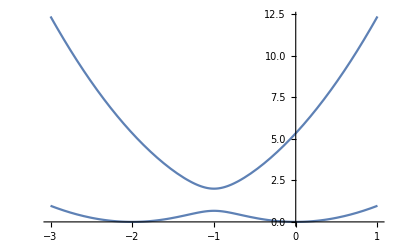

```mathematica
(*считал руками холестерик*)
(*σ=Subscript[k, 0]^2 ϵ,ν^2=A^2/ϵ^2*)
σ1=((ωp^2+ωm^2)- Sqrt[(ωp^2+ωm^2)^2-4(1-ν^2)ωp^2 ωm^2])/(2(1-ν^2))/.ωp->2q+ωm;
σ2=((ωp^2+ωm^2)+ Sqrt[(ωp^2+ωm^2)^2-4(1-ν^2)ωp^2 ωm^2])/(2(1-ν^2))/.ωp->2q+ωm;
Plot[{σ1,σ2}/.ν->0.5/.q->1,{ωm,-3,1}]
```

```mathematica
FullSimplify[Solve[Det[({{-(2+n)^2 1/σ+α, β}, {βc, -n^2 1/σ+γ}})]==0,σ]]
```

{{σ→(-n^2 α-(2+n)^2 γ+√((n^2 α+(2+n)^2 γ)^2+4 n^2 (2+n)^2 (β βc-α γ)))/(2 β βc-2 α γ)},{σ→-(n^2 α+(2+n)^2 γ+√((n^2 α+(2+n)^2 γ)^2+4 n^2 (2+n)^2 (β βc-α γ)))/(2 β βc-2 α γ)}}

```mathematica
(*обе ветви закона дисперсии в параметрах холестерика*)
```

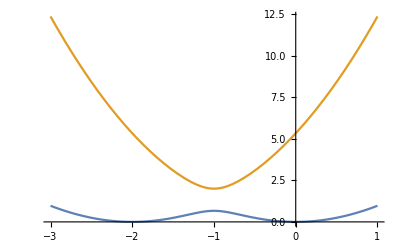
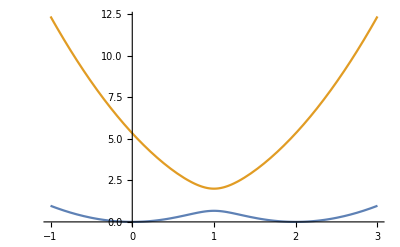

```mathematica
defintion ={α-> (e+Y) - (B ⅇ^(ⅈ (r-rc)) B)/(2e3),γ-> (e-Y) - (B ⅇ^(-ⅈ (r-rc))  B)/(2e3),β-> A -(B ⅇ^(ⅈ (r+rc))  B)/(2e3),βc-> A - (B ⅇ^(-ⅈ (r+rc))  B)/(2e3)};
cholpreset={e-> 1,e3-> 1, Y-> 0,B->0,Bc-> 0,r-> 0,rc-> 0,A-> 0.5};
σ1=(-n^2 α-(2+n)^2 γ+√((n^2 α+(2+n)^2 γ)^2+4 n^2 (2+n)^2 (β βc-α γ)))/(2 β βc-2 α γ)/.defintion/.cholpreset;
σ2=-(n^2 α+(2+n)^2 γ+√((n^2 α+(2+n)^2 γ)^2+4 n^2 (2+n)^2 (β βc-α γ)))/(2 β βc-2 α γ)/.defintion/.cholpreset;
σ11=(-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β βc-α γ)))/(2 β βc-2 α γ)/.defintion/.cholpreset;
σ22=(-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β βc-α γ)))/(2 β βc-2 α γ)/.defintion/.cholpreset;
{Plot[{σ1,σ2},{n,-3,1}],Plot[{σ11,σ22},{n,-1,3}]}
```

```mathematica
preset = {e-> 1,e3-> 1, Y-> 0,r->0,rc->0,A-> 0.5};
cholpreset={e-> 1,e3-> 1, Y-> 0,B->0,Bc-> 0,r-> 0,rc-> 0,A-> 0.5};
σ1=(-n^2 α-(2+n)^2 γ+√((n^2 α+(2+n)^2 γ)^2+4 n^2 (2+n)^2 (β βc-α γ)))/(2 β βc-2 α γ)/.defintion;
σ2=-(n^2 α+(2+n)^2 γ+√((n^2 α+(2+n)^2 γ)^2+4 n^2 (2+n)^2 (β βc-α γ)))/(2 β βc-2 α γ)/.defintion;
```

```mathematica
(*r-> x+ⅈ y*)
```

```mathematica
Manipulate[Plot[{(e3 ((2+n)^2 (B^2 ⅇ^(2 y)+2 e3 (-e+Y))+n^2 (B^2 ⅇ^(-2 y)-2 e3 (e+Y))+e3 √(1/e3^2((-4 e e3 (2+2 n+n^2)+B^2 ⅇ^(-2 y) (n^2+ⅇ^(4 y) (2+n)^2)+8 e3 (1+n) Y)^2+4 n^2 (2+n)^2 ((B^2 ⅇ^(-2 ⅈ x)-2 A e3) (B^2 ⅇ^(2 ⅈ x)-2 A e3)-(B^2 ⅇ^(2 y)+2 e3 (-e+Y)) (B^2 ⅇ^(-2 y)-2 e3 (e+Y)))))))/((B^2 ⅇ^(-2 ⅈ x)-2 A e3) (B^2 ⅇ^(2 ⅈ x)-2 A e3)-(B^2 ⅇ^(2 y)+2 e3 (-e+Y)) (B^2 ⅇ^(-2 y)-2 e3 (e+Y))),-((2 e3^2 ((2+n)^2 (e-(B^2 ⅇ^(2 y))/(2 e3)-Y)+n^2 (e-(B^2 ⅇ^(-2 y))/(2 e3)+Y)+1/2 √(1/e3^2((-4 e e3 (2+2 n+n^2)+B^2 ⅇ^(-2 y) (n^2+ⅇ^(4 y) (2+n)^2)+8 e3 (1+n) Y)^2+4 n^2 (2+n)^2 ((B^2 ⅇ^(-2 ⅈ x)-2 A e3) (B^2 ⅇ^(2 ⅈ x)-2 A e3)-(B^2 ⅇ^(2 y)+2 e3 (-e+Y)) (B^2 ⅇ^(-2 y)-2 e3 (e+Y)))))))/((B^2 ⅇ^(-2 ⅈ x)-2 A e3) (B^2 ⅇ^(2 ⅈ x)-2 A e3)-(B^2 ⅇ^(2 y)+2 e3 (-e+Y)) (B^2 ⅇ^(-2 y)-2 e3 (e+Y))))},{n,-3,1}],{B,0,2},{A,-0.5,1},{Y,0,1},{x,0, 2π},{y,0, π},{e,1,1},{e3,1,2}]
```

```mathematica
(*УРАВНЕНИЯ В ОБЩЕМ ВИДЕ В ТЕРМИНАХ тета*)

U2=({{1+(kp^2 Λ)/2, 1/2 kp^2 Λ}, {1/2  kp^2 Λ, 1+(kp^2 Λ)/2}});
U1=1/2 ⅈkp Λ Subscript[k, 0]^2({{(B ⅇ^(ⅈ (r+θ))+ⅇ^(-ⅈ (θ+Subscript[r, c])) Subscript[B, c]), ⅇ^(ⅈ (θ))  (B ⅇ^(ⅈ r)+ⅇ^(ⅈ Subscript[r, c]) Subscript[B, c])}, {ⅇ^(-ⅈ (θ)) (B ⅇ^(-ⅈ r)+ⅇ^(-ⅈ Subscript[r, c]) Subscript[B, c]), (B ⅇ^(-ⅈ (r+θ))+ⅇ^(ⅈ (θ+Subscript[r, c])) Subscript[B, c])}});
U0=({{1/2 (-kp^2+(2 (e+Y)) Subscript[k, 0]^2), 1/2 ( kp^2+(2 A ⅇ^(2 ⅈ θ)) Subscript[k, 0]^2)}, {1/2  kp^2+(A ⅇ^(-2 ⅈ θ)) Subscript[k, 0]^2, -kp^2/2+(e-Y) Subscript[k, 0]^2}});
U01=1/2 kp q Λ Subscript[B, c] Subscript[k, 0]^2({{ⅇ^(-ⅈ (θ+Subscript[r, c])), -ⅇ^(ⅈ (θ+Subscript[r, c]))}, {ⅇ^(-ⅈ (θ+Subscript[r, c])), - ⅇ^(ⅈ (θ+Subscript[r, c]))}});
U02=1/2 Λ B Subscript[B, c] Subscript[k, 0]^4({{-ⅇ^(ⅈ (r-Subscript[r, c])), -ⅇ^(ⅈ (r+2 θ+Subscript[r, c]))}, {-ⅇ^(-ⅈ (r+2 θ+Subscript[r, c])), -ⅇ^(-ⅈ (r-Subscript[r, c]))}});
ψ=({{ap[n] ⅇ^(ⅈ θ n)}, {am[n] ⅇ^(ⅈ θ n)}});
```

```mathematica
tmp=U02.({{ap[n] ⅇ^(ⅈ θ n)}, {am[n] ⅇ^(ⅈ θ n)}})//MatrixForm;
```

```mathematica
L2=q^2({{- n^2 (1+(kp^2 Λ)/2) ap[n], -1/2  kp^2 n^2 Λ am[n]}, {-1/2  kp^2 n^2 Λ ap[n], - n^2 (1+(kp^2 Λ)/2) am[n]}});
L1=q kp Λ Subscript[k, 0]^2({{-1/2   (B ⅇ^(ⅈ r) (+n) ap[-1+n]+(n) ap[1+n] Subscript[B, c] ⅇ^(-ⅈ Subscript[r, c])), -1/2 (+n)  am[-1+n] (B ⅇ^(ⅈ r)+ⅇ^(ⅈ Subscript[r, c]) Subscript[B, c])}, {-1/2 ⅇ^(-ⅈ (r+Subscript[r, c]))(+n)ap[1+n] (B ⅇ^(ⅈ Subscript[r, c])+ⅇ^(ⅈ r) Subscript[B, c]), -1/2  (B ⅇ^(-ⅈ r) (+n) am[1+n]+ (+n) am[-1+n] Subscript[B, c] ⅇ^(ⅈ Subscript[r, c]))}});
L0=({{1/2  ap[n] (-kp^2+2 (e+Y) Subscript[k, 0]^2), 1/2(kp^2 am[n]+am[n-2]2 A  Subscript[k, 0]^2)}, {(kp^2/2 ap[n]+ap[n+2]A  Subscript[k, 0]^2), am[n] (-kp^2/2+(e-Y) Subscript[k, 0]^2)}});
L01=kp q Λ Subscript[B, c] Subscript[k, 0]^2({{1/2 ⅇ^(-ⅈ (Subscript[r, c]))  ap[n+1], -1/2 ⅇ^(ⅈ (Subscript[r, c]))  am[n-1]}, {1/2 ⅇ^(-ⅈ (Subscript[r, c]))  ap[n+1], -1/2 ⅇ^(ⅈ (Subscript[r, c]))  am[n-1]}});
L02=Λ B Subscript[B, c] Subscript[k, 0]^4({{-1/2  ⅇ^(+ⅈ (r-Subscript[r, c]))  ap[n], -1/2  ⅇ^(+ⅈ (r+Subscript[r, c]))  am[n-2]}, {-1/2  ⅇ^(-ⅈ (r+Subscript[r, c]))  ap[n+2], -1/2  ⅇ^(-ⅈ (r-Subscript[r, c]))  am[n]}});
```

```mathematica
expr=L2.({{1}, {1}})+L1.({{1}, {1}})+L0.({{1}, {1}})+L01.({{1}, {1}})+L02.({{1}, {1}});
```

```mathematica
Kt={Coefficient[expr[[1]],ap[n]][[1]],Coefficient[expr[[1]],am[n]][[1]]};
Lt={Coefficient[expr[[1]],ap[n-1]][[1]],Coefficient[expr[[1]],am[n-1]][[1]]};
Mt={Coefficient[expr[[1]],ap[n+1]][[1]],Coefficient[expr[[1]],am[n+1]][[1]]};
Nt={Coefficient[expr[[1]],ap[n-2]][[1]],Coefficient[expr[[1]],am[n-2]][[1]]};
Pt={Coefficient[expr[[1]],ap[n+2]][[1]],Coefficient[expr[[1]],am[n+2]][[1]]};
Kd={Coefficient[expr[[2]],ap[n]][[1]],Coefficient[expr[[2]],am[n]][[1]]};
Ld={Coefficient[expr[[2]],ap[n-1]][[1]],Coefficient[expr[[2]],am[n-1]][[1]]};
Md={Coefficient[expr[[2]],ap[n+1]][[1]],Coefficient[expr[[2]],am[n+1]][[1]]};
Nd={Coefficient[expr[[2]],ap[n-2]][[1]],Coefficient[expr[[2]],am[n-2]][[1]]};
Pd={Coefficient[expr[[2]],ap[n+2]][[1]],Coefficient[expr[[2]],am[n+2]][[1]]};
```

```mathematica
Kt.{ap[n],am[n]}+Lt.{ap[n-1],am[n-1]}+Mt.{ap[n+1],am[n+1]}+Nt.{ap[n-2],am[n-2]}+Pt.{ap[n+2],am[n+2]}-expr[[1]]//Simplify
Kd.{ap[n],am[n]}+Ld.{ap[n-1],am[n-1]}+Md.{ap[n+1],am[n+1]}+Nd.{ap[n-2],am[n-2]}+Pd.{ap[n+2],am[n+2]}-expr[[2]]//Simplify
```

{0}

{0}

```mathematica
Kt/.n-> n+2
```

{-(2+n)^2 q^2 (1+(kp^2 Λ)/2)-1/2 B ⅇ^(ⅈ (r-r_c)) Λ B_c k_0^4+1/2 (-kp^2+2 (e+Y) k_0^2),kp^2/2-1/2 kp^2 (2+n)^2 q^2 Λ}

```mathematica
HO={ap[n+2]-> 0,ap[n-2]-> 0,am[n]-> 0,am[n-4]-> 0,am[1+n]-> 0,ap[-3+n]-> 0};
```

```mathematica
T=Kt.{ap[n],am[n]}+Lt.{ap[n-1],am[n-1]}+Mt.{ap[n+1],am[n+1]}+Nt.{ap[n-2],am[n-2]}+Pt.{ap[n+2],am[n+2]}/.n-> n;
Tp=Kt.{ap[n],am[n]}+Lt.{ap[n-1],am[n-1]}+Mt.{ap[n+1],am[n+1]}+Nt.{ap[n-2],am[n-2]}+Pt.{ap[n+2],am[n+2]}/.n-> n+1;
Tm=Kt.{ap[n],am[n]}+Lt.{ap[n-1],am[n-1]}+Mt.{ap[n+1],am[n+1]}+Nt.{ap[n-2],am[n-2]}+Pt.{ap[n+2],am[n+2]}/.n-> n-1;
d=Kd.{ap[n],am[n]}+Ld.{ap[n-1],am[n-1]}+Md.{ap[n+1],am[n+1]}+Nd.{ap[n-2],am[n-2]}+Pd.{ap[n+2],am[n+2]}/.n-> n-2;
dp=Kd.{ap[n],am[n]}+Ld.{ap[n-1],am[n-1]}+Md.{ap[n+1],am[n+1]}+Nd.{ap[n-2],am[n-2]}+Pd.{ap[n+2],am[n+2]}/.n-> n-1;
dm=Kd.{ap[n],am[n]}+Ld.{ap[n-1],am[n-1]}+Md.{ap[n+1],am[n+1]}+Nd.{ap[n-2],am[n-2]}+Pd.{ap[n+2],am[n+2]}/.n-> n-3;
```

```mathematica
eq1=Normal[Series[T,{kp,0,1}]]/.HO;
eq2=Normal[Series[Tp,{kp,0,1}]]/.HO;
eq3=Normal[Series[Tm,{kp,0,1}]]/.HO;
eq4=Normal[Series[d,{kp,0,1}]]/.HO;
eq5=Normal[Series[dp,{kp,0,1}]]/.HO;
eq6=Normal[Series[dm,{kp,0,1}]]/.HO;
```

```mathematica
Mat=CoefficientArrays[{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0},{ap[n],am[n-2],ap[n+1],am[n-1],ap[n-1],am[n-3]}][[2]]//Normal;
MatrixForm[Mat]
```

(-n^2 q^2+(e+Y) k_0^2-1/2 B ⅇ^(ⅈ (r-r_c)) Λ B_c k_0^4 | A k_0^2-1/2 B ⅇ^(ⅈ (r+r_c)) Λ B_c k_0^4 | -1/2 ⅇ^(-ⅈ r_c) kp (-1+n) q Λ B_c k_0^2 | -1/2 kp q Λ (B ⅇ^(ⅈ r) n+ⅇ^(ⅈ r_c) B_c+ⅇ^(ⅈ r_c) n B_c) k_0^2 | -1/2 B ⅇ^(ⅈ r) kp n q Λ k_0^2 | 0
-1/2 B ⅇ^(ⅈ r) kp (1+n) q Λ k_0^2 | 0 | -(1+n)^2 q^2+(e+Y) k_0^2-1/2 B ⅇ^(ⅈ (r-r_c)) Λ B_c k_0^4 | A k_0^2-1/2 B ⅇ^(ⅈ (r+r_c)) Λ B_c k_0^4 | 0 | 0
-1/2 ⅇ^(-ⅈ r_c) kp (-2+n) q Λ B_c k_0^2 | -1/2 kp q Λ (-B ⅇ^(ⅈ r)+B ⅇ^(ⅈ r) n+ⅇ^(ⅈ r_c) n B_c) k_0^2 | 0 | 0 | -(-1+n)^2 q^2+(e+Y) k_0^2-1/2 B ⅇ^(ⅈ (r-r_c)) Λ B_c k_0^4 | A k_0^2-1/2 B ⅇ^(ⅈ (r+r_c)) Λ B_c k_0^4
A k_0^2-1/2 B ⅇ^(-ⅈ (r+r_c)) Λ B_c k_0^4 | -(-2+n)^2 q^2+(e-Y) k_0^2-1/2 B ⅇ^(-ⅈ (r-r_c)) Λ B_c k_0^4 | 0 | -1/2 B ⅇ^(-ⅈ r) kp (-2+n) q Λ k_0^2 | kp (1/2 ⅇ^(-ⅈ r_c) q Λ B_c k_0^2-1/2 ⅇ^(-ⅈ (r+r_c)) (-2+n) q Λ (B ⅇ^(ⅈ r_c)+ⅇ^(ⅈ r) B_c) k_0^2) | -1/2 ⅇ^(ⅈ r_c) kp (-1+n) q Λ B_c k_0^2
kp (1/2 ⅇ^(-ⅈ r_c) q Λ B_c k_0^2-1/2 ⅇ^(-ⅈ (r+r_c)) (-1+n) q Λ (B ⅇ^(ⅈ r_c)+ⅇ^(ⅈ r) B_c) k_0^2) | -1/2 ⅇ^(ⅈ r_c) kp n q Λ B_c k_0^2 | A k_0^2-1/2 B ⅇ^(-ⅈ (r+r_c)) Λ B_c k_0^4 | -(-1+n)^2 q^2+(e-Y) k_0^2-1/2 B ⅇ^(-ⅈ (r-r_c)) Λ B_c k_0^4 | 0 | 0
0 | -1/2 B ⅇ^(-ⅈ r) kp (-3+n) q Λ k_0^2 | 0 | 0 | A k_0^2-1/2 B ⅇ^(-ⅈ (r+r_c)) Λ B_c k_0^4 | -(-3+n)^2 q^2+(e-Y) k_0^2-1/2 B ⅇ^(-ⅈ (r-r_c)) Λ B_c k_0^4)

```mathematica
Mat0=({{-n^2 τ+α, β, -1/2 ⅇ^(-ⅈ Subscript[r, c]) kp (-1+n) q Λ Subscript[B, c], -1/2 kp q Λ (B ⅇ^(ⅈ r) n+ⅇ^(ⅈ Subscript[r, c]) Subscript[B, c]+ⅇ^(ⅈ Subscript[r, c]) n Subscript[B, c]), -1/2 B ⅇ^(ⅈ r) kp n q Λ, 0}, {-1/2 B ⅇ^(ⅈ r) kp (1+n) q Λ, 0, -(1+n)^2 τ+α, β, 0, 0}, {-1/2 ⅇ^(-ⅈ Subscript[r, c]) kp (-2+n) q Λ Subscript[B, c], -1/2 kp q Λ (-B ⅇ^(ⅈ r)+B ⅇ^(ⅈ r) n+ⅇ^(ⅈ Subscript[r, c]) n Subscript[B, c]), 0, 0, -(-1+n)^2 τ+α, β}, {βc, -(-2+n)^2 τ+γ, 0, -1/2 B ⅇ^(-ⅈ r) kp (-2+n) q Λ, kp (1/2 ⅇ^(-ⅈ Subscript[r, c]) q Λ Subscript[B, c]-1/2 ⅇ^(-ⅈ (r+Subscript[r, c])) (-2+n) q Λ (B ⅇ^(ⅈ Subscript[r, c])+ⅇ^(ⅈ r) Subscript[B, c]) ), -1/2 ⅇ^(ⅈ Subscript[r, c]) kp (-1+n) q Λ Subscript[B, c]}, {kp (1/2 ⅇ^(-ⅈ Subscript[r, c]) q Λ Subscript[B, c] -1/2 ⅇ^(-ⅈ (r+Subscript[r, c])) (-1+n) q Λ (B ⅇ^(ⅈ Subscript[r, c])+ⅇ^(ⅈ r) Subscript[B, c]) ), -1/2 ⅇ^(ⅈ Subscript[r, c]) kp n q Λ Subscript[B, c], βc, -(-1+n)^2 τ+γ, 0, 0}, {0, -1/2 B ⅇ^(-ⅈ r) kp (-3+n) q Λ, 0, 0, βc, -(-3+n)^2 τ+γ}});
```

```mathematica
tm=Mat0.{ap[n],am[n-2],ap[n+1],am[n-1],ap[n-1],am[n-3]};
solu1=Solve[{tm[[1]]==0,tm[[2]]==0,tm[[3]]==0,tm[[5]]==0,tm[[6]]==0},{am[n-2],ap[n+1],am[n-1],ap[n-1],am[n-3]}];
```

```mathematica
Series[{am[n-2],ap[n+1],am[n-1],ap[n-1],am[n-3]}/.solu1,{kp,0,1}]//FullSimplify//Normal
```

{{((-α+n^2 τ) ap[n])/β,(ⅇ^(-ⅈ (r+r_c)) kp q Λ ap[n] (B ⅇ^(ⅈ r_c) ((-1+n) β+ⅇ^(2 ⅈ r) (1+n) (-γ+(-1+n)^2 τ))+ⅇ^(ⅈ r) ((-2+n) β+ⅇ^(2 ⅈ r_c) n (-α+n^2 τ)) B_c))/(2 (β βc+(-γ+(-1+n)^2 τ) (α-(1+n)^2 τ))),(ⅇ^(-ⅈ (r+r_c)) kp q Λ ap[n] (B ⅇ^(ⅈ r_c) β (α-n α+(1+n) (ⅇ^(2 ⅈ r) βc+(-1+n^2) τ))+ⅇ^(ⅈ r) (-α+(1+n)^2 τ) ((-2+n) β+ⅇ^(2 ⅈ r_c) n (-α+n^2 τ)) B_c))/(2 β (β βc+(-γ+(-1+n)^2 τ) (α-(1+n)^2 τ))),(ⅇ^(-ⅈ (r+r_c)) kp q Λ ap[n] (B ⅇ^(ⅈ r_c) (-α+n^2 τ) ((-3+n) β+ⅇ^(2 ⅈ r) (-1+n) (-γ+(-3+n)^2 τ))+ⅇ^(ⅈ r) (-γ+(-3+n)^2 τ) ((-2+n) β+ⅇ^(2 ⅈ r_c) n (-α+n^2 τ)) B_c))/(2 β (β βc+(-γ+(-3+n)^2 τ) (α-(-1+n)^2 τ))),(ⅇ^(-ⅈ (r+r_c)) kp q Λ ap[n] (B ⅇ^(ⅈ r_c) (α-n^2 τ) (-ⅇ^(2 ⅈ r) (-1+n) βc+(-3+n) (α-(-1+n)^2 τ))+ⅇ^(ⅈ r) βc ((-2+n) β+ⅇ^(2 ⅈ r_c) n (-α+n^2 τ)) B_c))/(2 β (β βc+(-γ+(-3+n)^2 τ) (α-(-1+n)^2 τ)))}}

```mathematica
def={γ-> (e-Y)-1/2 B ⅇ^(-ⅈ (r-Subscript[r, c])) Λ Subscript[B, c] Subscript[k, 0]^2,βc-> A-1/2 B ⅇ^(-ⅈ (r+Subscript[r, c])) Λ Subscript[B, c] Subscript[k, 0]^2,β->A-1/2 B ⅇ^(ⅈ (r+Subscript[r, c])) Λ Subscript[B, c] Subscript[k, 0]^2,α-> (e+Y)-1/2 B ⅇ^(ⅈ (r-Subscript[r, c])) Λ Subscript[B, c] Subscript[k, 0]^2,σ-> q^2/Subscript[k, 0]^2 };
```

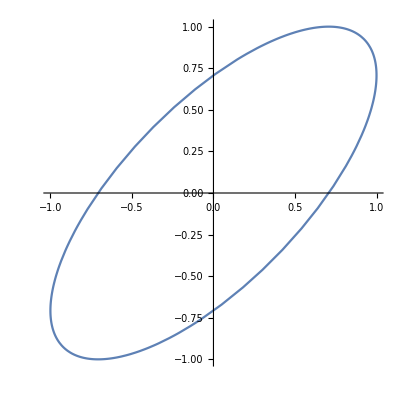

```mathematica
ParametricPlot[{Cos[t-Pi/4],Cos[t]},{t,0,2 Pi}]
```

```mathematica
Mat00=({{-n^2 (τ+kp δ)+α, β, 0, 0, 0, 0}, {-1/2 B ⅇ^(ⅈ r) kp (1+n) q Λ, 0, -(1+n)^2 τ+α, β, 0, 0}, {-1/2 ⅇ^(-ⅈ Subscript[r, c]) kp (-2+n) q Λ Subscript[B, c], -1/2 kp q Λ (-B ⅇ^(ⅈ r)+B ⅇ^(ⅈ r) n+ⅇ^(ⅈ Subscript[r, c]) n Subscript[B, c]), 0, 0, -(-1+n)^2 τ+α, β}, {βc, -(-2+n)^2 (τ+kp δ)+γ, 0, 0, 0, 0}, {kp (1/2 ⅇ^(-ⅈ Subscript[r, c]) q Λ Subscript[B, c] -1/2 ⅇ^(-ⅈ (r+Subscript[r, c])) (-1+n) q Λ (B ⅇ^(ⅈ Subscript[r, c])+ⅇ^(ⅈ r) Subscript[B, c]) ), -1/2 ⅇ^(ⅈ Subscript[r, c]) kp n q Λ Subscript[B, c], βc, -(-1+n)^2 τ+γ, 0, 0}, {0, -1/2 B ⅇ^(-ⅈ r) kp (-3+n) q Λ, 0, 0, βc, -(-3+n)^2 τ+γ}});
```

```mathematica
eqs=Mat00.{ap[n]+kp ap1[n],am[n-2]+kp am1[n-2],kp ap[n+1],kp am[n-1],kp ap[n-1],kp am[n-3]};
```

```mathematica
Normal[Series[eqs,{kp,0,0}]]//Normal//MatrixForm;
Solve[Normal[Series[eqs,{kp,0,1}]]-Normal[Series[eqs,{kp,0,0}]]==0,{ap1[n],am1[n-2],ap[n+1],am[n-1],ap[n-1],am[n-3]}]//Simplify
```

{{ap1[n]→(δ ((-2+n)^2 β am[-2+n]+n^2 (-γ+(-2+n)^2 τ) ap[n]))/(β βc+(-γ+(-2+n)^2 τ) (α-n^2 τ)),am1[-2+n]→(δ ((-2+n)^2 (-α+n^2 τ) am[-2+n]+n^2 βc ap[n]))/(β βc+(-γ+(-2+n)^2 τ) (α-n^2 τ)),ap[1+n]→(ⅇ^(-ⅈ (r+r_c)) q Λ (ⅇ^(ⅈ (r+2 r_c)) n β am[-2+n] B_c+ap[n] (B ⅇ^(ⅈ r_c) ((-1+n) β+ⅇ^(2 ⅈ r) (1+n) (-γ+(-1+n)^2 τ))+ⅇ^(ⅈ r) (-2+n) β B_c)))/(2 (β βc+(-γ+(-1+n)^2 τ) (α-(1+n)^2 τ))),am[-1+n]→(ⅇ^(-ⅈ (r+r_c)) q Λ (ⅇ^(ⅈ (r+2 r_c)) n (-α+(1+n)^2 τ) am[-2+n] B_c+ap[n] (-B ⅇ^(ⅈ r_c) ((-1+n) α-(1+n) (ⅇ^(2 ⅈ r) βc+(-1+n^2) τ))+ⅇ^(ⅈ r) (-2+n) (-α+(1+n)^2 τ) B_c)))/(2 (β βc+(-γ+(-1+n)^2 τ) (α-(1+n)^2 τ))),ap[-1+n]→-(q Λ (-B ⅇ^(-ⅈ r) (-3+n) β am[-2+n]+ⅇ^(-ⅈ r_c) (γ-(-3+n)^2 τ) ((-2+n) ap[n] B_c+ⅇ^(ⅈ r_c) am[-2+n] (B ⅇ^(ⅈ r) (-1+n)+ⅇ^(ⅈ r_c) n B_c))))/(2 (β βc-(γ-(-3+n)^2 τ) (α-(-1+n)^2 τ))),am[-3+n]→(ⅇ^(-ⅈ (r+r_c)) q Λ (ⅇ^(ⅈ r) (-2+n) βc ap[n] B_c+ⅇ^(ⅈ r_c) am[-2+n] (-B (-3+n) α+B (-1+n) (ⅇ^(2 ⅈ r) βc+(3-4 n+n^2) τ)+ⅇ^(ⅈ (r+r_c)) n βc B_c)))/(2 (β βc+(-γ+(-3+n)^2 τ) (α-(-1+n)^2 τ)))}}

```mathematica
Solve[Coefficient[Det[Mat00],kp,1]==0,δ]//Simplify
```

{{δ→0}}

```mathematica
(kp q Λ ap[n] (B  β (α-n α+(1+n) (ⅇ^(ⅈ r) βc+ⅇ^(-ⅈ (r))(-1+n^2) τ))+ (-α+(1+n)^2 τ) ((-2+n) β ⅇ^(-ⅈ (Subscript[r, c]))+ⅇ^(ⅈ Subscript[r, c]) n (-α+n^2 τ)) Subscript[B, c]))/(2 β (β βc+(-γ+(-1+n)^2 τ) (α-(1+n)^2 τ)))
(kp q Λ ap[n] (B (-α+n^2 τ) ((-3+n) β ⅇ^(-ⅈ (r))+ⅇ^(ⅈ r)  (-1+n) (-γ+(-3+n)^2 τ))+ (-γ+(-3+n)^2 τ) ((-2+n) β ⅇ^(-ⅈ (Subscript[r, c]))+ⅇ^(ⅈ Subscript[r, c]) n (-α+n^2 τ)) Subscript[B, c]))/(2 β (β βc+(-γ+(-3+n)^2 τ) (α-(-1+n)^2 τ)))
(kp q Λ ap[n] (B  (α-n^2 τ) (-ⅇ^(ⅈ r)  (-1+n) βc+ⅇ^(-ⅈ (r))(-3+n) (α-(-1+n)^2 τ))+ βc ((-2+n) β ⅇ^(-ⅈ (Subscript[r, c]))+ⅇ^(ⅈ Subscript[r, c]) n (-α+n^2 τ)) Subscript[B, c]))/(2 β (β βc+(-γ+(-3+n)^2 τ) (α-(-1+n)^2 τ)))
```

```mathematica
TeXForm[  (B  (α-n^2 τ) (-ⅇ^(ⅈ r)  (-1+n) βc+ⅇ^(-ⅈ (r))(-3+n) (α-(-1+n)^2 τ))+ βc ((-2+n) β ⅇ^(-ⅈ (Subscript[r, c]))+ⅇ^(ⅈ Subscript[r, c]) n (-α+n^2 τ)) Subscript[B, c])]
```

\text{$\beta $c} B_c \left(n e^{i r_c} \left(n^2 \tau -\alpha \right)+\beta  (n-2) e^{-i r_c}\right)+B \left(\alpha -n^2 \tau \right)
   \left((n-3) e^{-i r} \left(\alpha -(n-1)^2 \tau \right)-\text{$\beta $c} (n-1) e^{i r}\right)

```mathematica
FullSimplify[ kp q Λ ap[n] (B  β (α-n α+(1+n) (ⅇ^(ⅈ r) βc+ⅇ^(-ⅈ (r))(-1+n^2) τ))+ (-α+(1+n)^2 τ) ((-2+n) β ⅇ^(-ⅈ (Subscript[r, c]))+ⅇ^(ⅈ Subscript[r, c]) n (-α+n^2 τ)) Subscript[B, c])]
```

kp q Λ ap[n] (B β (α-n α+ⅇ^(-ⅈ r) (1+n) (ⅇ^(2 ⅈ r) βc+(-1+n^2) τ))+ⅇ^(-ⅈ r_c) (-α+(1+n)^2 τ) ((-2+n) β+ⅇ^(2 ⅈ r_c) n (-α+n^2 τ)) B_c)